## Black hole bombs: direct integration from horizon to mirror radius

```mathematica
ar=8/10;
M=1;
l=1;
m=1;
s=0;
rminus=M-Sqrt[M^2-ar^2];rplus=M+Sqrt[M^2-ar^2];
Delta=(r-rplus)*(r-rminus);Delta1=D[Delta,r];
bb=Delta1/.r->rplus;
cc=(rplus^2+ar^2)/bb;
Omega=ar/(rplus^2+ar^2);
f=Delta/(r^2+ar^2);f1=D[f,r];
fa0=l(l+1);
fa1=0;
fa2=-1-(l (l^2-Abs[m]^2))/(2 (-1/2+l) (1/2+l))+((1+l) ((1+l)^2-Abs[m]^2))/(2 (1/2+l) (3/2+l));
fa3=0;
fa4=(-6+34 l+4 l^2-52 l^3-6 l^4+24 l^5+8 l^6+(-60+52 l+4 l^2-96 l^3-48 l^4) Abs[m]^2+(66+40 l+40 l^2) Abs[m]^4)/((-15+4 l+4 l^2) (-3+4 l+4 l^2)^3);
Alm=fa0+fa1 ar*w+ fa2(ar*w)^2+fa3(ar*w)^3+fa4(ar*w)^4;
lambda=Alm+ar^2*w^2-2*ar*m*w;
Vscalar=(w-ar*m/(r^2+ar^2))^2-Delta*(lambda*(r^2+ar^2)^2+2*M*r^3+ar^2*r^2-4*M*ar^2*r+ar^4)/(r^2+ar^2)^4;
EQ=f^2 ψ''[r]+f1*f*ψ'[r]+Vscalar*ψ[r];rsint=Integrate[1/f,r];imaginary=Im[rsint]/.r->20*rplus;rs=rsint-imaginary*I;rs/.r->10*rplus//N;
```

```mathematica
INT[w0_,rinfini_,EPS0_]:=(
param={w->w0};
EPS=EPS0;
rinf=rinfini;
rhn=(1+EPS)rplus;
(****INTEGRATION FROM THE HORIZON***)
ψgH=(r-rplus)^(-I*cc*(w-m*Omega))//.param;
BCs={ψ[rhn]==ψgH/.r->rhn,ψ'[rhn]==D[ψgH,r]/.r->rhn};
EQs={Vscalar ψ[r]+f1*f ψ'[r]+f^2 ψ''[r]==0}/.param;
solH=NDSolve[Union[EQs,BCs],ψ,{r,rhn,rinf}];
(*******)
ψnINF=ψ[rinf]/.solH[[1]];
{ψnINF}
);
```

```mathematica
wguess=0.1+10^(-6)*I;

ii=0;
NMAX=400;
While[ii<NMAX+1,

rinfinity=50-0.1*ii;
f4[y_?NumericQ]:=INT[y,rinfinity,10^-6][[1]];
y0n=y/.FindRoot[f4[y]==0,{y,wguess}][[1]];
wguess=y0n;
answer[ii]={rinf,Re[y0n],Im[y0n]};ii++];
answer[0]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{50.,0.0850546,7.01735×10^-7}

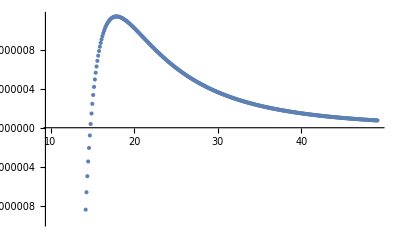

```mathematica
Tabe=Table[answer[ii],{ii,0,NMAX}];
Tab1=Table[{Tabe[[i,1]],Tabe[[i,3]]},{i,10,Length[Tabe]}];ListPlot[Tab1]
```

## Massive-scalar-field instability

```mathematica
INT[w_,mu_,ar_,l_,m_,s_,NITMAX_]:=(
M=1;
br=Sqrt[1-ar^2];
rminus=(1-br);
rplus=1+br;
k1=1/2*Abs[m-s];
k2=1/2*Abs[m+s];
OmegaH=ar/(2*M*rplus);
Alm=SpheroidalEigenvalue[l,m,I ar √(w^2-mu^2)]-ar^2 (w^2-mu^2);

Clear[α,β,γ];
q=-Sqrt[mu^2-w^2];
c0=1-2*I*w-2*I/br*(w-ar*m/2);
c1=-4+4*I*(w-I*q*(1+br))+4*I/br*(w-ar*m/2)-2*(w^2+q^2)/q;
c2=3-2*I*w-2*I/br*(w-ar*m/2)-2*(q^2-w^2)/q;c3=2*I*(w-I*q)^3/q+2*(w-I*q)^2*br+q^2*ar^2+2*I*q*ar*m-Alm-1-(w-I*q)^2/q+2*q*br+2*I/br*((w-I*q)^2/q+1)*(w-ar*m/2);c4=(w-I*q)^4/q^2+2*I*w*(w-I*q)^2/q-2*I/br*(w-I*q)^2/q*(w-ar*m/2);γ=Function[n,n^2+(c2-3)*n+c4+(-c2+2)*0];
β=Function[n,-2*n^2+(c1+2)*n+c3];
α=Function[n,n^2+(c0+1)*n+c0];

Leaver31=Module[{Rn},For[{n=NITMAX;Rn=-1.0;},n>0,{Rn=γ[n]/(β[n]-α[n]*Rn);n--;}
];Rn];

β[0]/α[0]-Leaver31
)
```

```mathematica
mu0=0.42;
a0=0.99;
l0=1;
m0=1;
N0=1000;
wguess=0.41+1*10^(-9)*I;

f[x_?NumberQ]:=INT[x,mu0,a0,l0,m0,0,N0];
root=x/.FindRoot[f[x],{x,wguess}];
check=Abs[f[root]];
{root,check}
```

{0.408806+1.50386×10^-7 ⅈ,4.52019×10^-12}

## References

```mathematica
[1]Press and Teukolsky , "Floating orbits, superradiant scattering and the black hole bomb", Nature 238 (1972) 211 
[2]V. Cardoso, J. P. S. Lemos, O. J. C. Dias and S. Yoshida, "The black hole bomb and superradiant instabilities", Phys.Rev D70 (2004) 049903
[3] R. Brito, V. Cardoso and P. Pani,  "Superradiance", Lecture Notes in Physics 906 (2015)
```

```mathematica
[6]https://centra.tecnico.ulisboa.pt/network/grit/files/
```